```mathematica
ClearAll["Global`*"]
```

### Numerical implementation

```mathematica
Tcore[I_,A1_,A2_,A3_]:=I/2(A1+A2)+A3*I^2;
Tsp[j_,A1_,A2_,A3_,V_,gm_]:=j/2(A2+A3)+A1*j^2-V*(2j-1)/(j+1)Sin[gm*π/180+π/6];
Aphi[phi_,A1_,A2_,A3_]:=A1*Cos[phi]^2+A2*Sin[phi]^2-A3;
Hmin[theta_,phi_,I_,j_,A1_,A2_,A3_,V_,gm_]:=I(I-1/2)Sin[theta]^2*Aphi[phi,A1,A2,A3]-2*A1*I*j*Sin[theta]+Tcore[I,A1,A2,A3]+Tsp[j,A1,A2,A3,V,gm];
Ak[moi_]:=1/(2*moi);
```

```mathematica
I1fit=72;I2fit=15;I3fit=7;
Vfit=2.1;gmfit=22;
j1=13/2;
A1fit=Ak[I1fit];A2fit=Ak[I2fit];A3fit=Ak[I3fit];
Hpolar[theta_,phi_,I_]:=Hmin[theta,phi,I,j1,A1fit,A2fit,A3fit,Vfit,gmfit];
m2={π/2,0};
Hminimal[I_]:=Hpolar[m2[[1]],m2[[2]],I];
Htheta[I_]:=Table[{x,Hpolar[x,m2[[2]],I]},{x,0,π,0.05}];
Hphi[I_]:=Table[{y,Hpolar[m2[[1]],y,I]},{y,0,2π,0.05}];
```

```mathematica
imageFeatures={Frame->True,Axes->False,AspectRatio->0.8,ImageSize->380,FrameStyle->Directive[Black],LabelStyle->{17,FontFamily->"Latin Modern Roman",Black}};
texStyle={FontFamily->"Latin Modern Roman",Black,17};
```

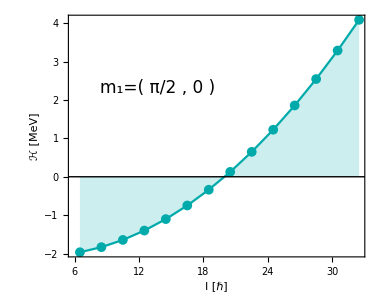

```mathematica
figure=ListPlot[Table[{s,Hminimal[s]},{s,6.5,32.5,2}],Frame->True,Axes->False,AspectRatio->0.8,ImageSize->380,FrameStyle->Directive[Black],PlotRange->All,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->Darker@Cyan,FrameLabel->{"I [ℏ]","ℋ [MeV]"},Evaluate[imageFeatures],Filling->0];
gfx=Show[{figure,Graphics[{Black,Line[{{-1,0},{40,0}}]}],Graphics[Inset[Style["m_1=( π/2 , 0 )",Evaluate[texStyle]],Scaled[{0.3,0.7}]]]}];
Export["/Users/basavyr/Documents/Work/PhD/163Lu-New-TSD4-Formalism/Code/Update-July-2022/plots/H-minimal-m1.pdf",Show[gfx],ImageResolution->1200];
gfx
```

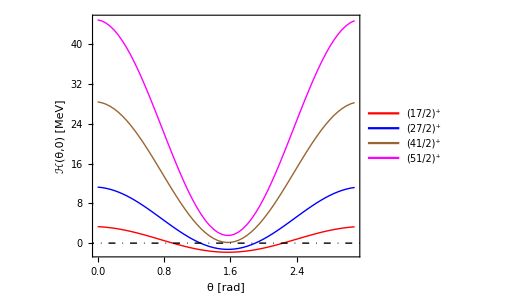

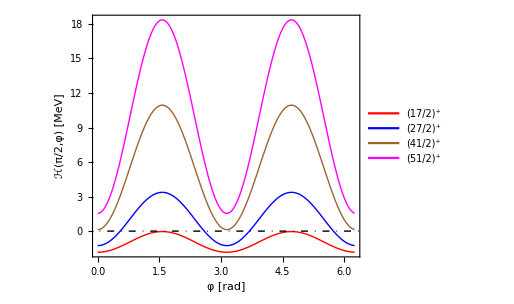

```mathematica
thetaplot=ListPlot[{Htheta[17/2],Htheta[27/2],Htheta[41/2],Htheta[51/2]},Evaluate[imageFeatures],Joined->True,FrameLabel->{"θ [rad]","ℋ(θ,0) [MeV]"},PlotLegends->Placed[{"(17/2)^+","(27/2)^+","(41/2)^+","(51/2)^+"},{0.5,0.65}],PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Brown},{Thick,Magenta}}];
gfx2=Show[{thetaplot,Graphics[{Black,DotDashed,Line[{{-1,0},{40,0}}]}]}];
gfx2
Export["/Users/basavyr/Documents/Work/PhD/163Lu-New-TSD4-Formalism/Code/Update-July-2022/plots/H-minimal-m1-theta.pdf",Show[gfx2],ImageResolution->1200];
phiplot=ListPlot[{Hphi[17/2],Hphi[27/2],Hphi[41/2],Hphi[51/2]},Evaluate[imageFeatures],Joined->True,FrameLabel->{"φ [rad]","ℋ(π/2,φ) [MeV]"},PlotLegends->Placed[{"(17/2)^+","(27/2)^+","(41/2)^+","(51/2)^+"},{0.51,0.69}],PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Brown},{Thick,Magenta}}];
gfx3=Show[{phiplot,Graphics[{Black,DotDashed,Line[{{-1,0},{40,0}}]}]}];
gfx3
Export["/Users/basavyr/Documents/Work/PhD/163Lu-New-TSD4-Formalism/Code/Update-July-2022/plots/H-minimal-m1-phi.pdf",Show[gfx3],ImageResolution->1200];
```